```mathematica
Parametric Analysis of second order systems of linear 
differential equations
```

```mathematica
Given a generic second order system of the form:
Ẋ = AX  
where "A" is called the characteristic matrix of the system of the form:
A=[{{a, b}, {c, d}}], Ẋ and X are vectors of 1x 2. Then we calculate eigenvalues with:
Det(A - λI ) =λ^2 - (a + d) λ + (a*d - b*c), finally we have, Subscript[λ, 1,2]=(a+d)/2±(√((a+d)^2-4(a*d-b*c)))/2
in order to Analize, second order system we must consider following cases:
```

Spiral Sink (a+d)^2-4(a*d-b*c) < 0 and (a+d) < 0

```mathematica
Reduce[(a+d)^2 - 4(a*d-b*c)<0 &&(a+d)<0,{a,b,c,d}, Reals]
```

```mathematica
(delta&&(fi||alfa))||beta
```

Nodal Sink (a+d)^2-4(a*d-b*c) > 0 and (λ_1)(λ_2) > 0 and (λ_1)+(λ_2)<0

```mathematica
Reduce[(a+d)^2 - 4(a*d-b*c)>0 && ((a +d)/2 + Sqrt[(a+d)^2 - 4(a*d-b*c)]/2) * ((a +d)/2 - Sqrt[(a+d)^2 - 4(a*d-b*c)]/2) > 0 && ((a +d)/2 + Sqrt[(a+d)^2 - 4(a*d-b*c)]/2) + ((a +d)/2 - Sqrt[(a+d)^2 - 4(a*d-b*c)]/2) < 0,{a,b,c,d}, Reals]
```

```mathematica
rho||beta||alpha
```

Spiral Source (a+d)^2-4(a*d-b*c) < 0 and (a+d) > 0

```mathematica
Reduce[(a+d)^2 - 4(a*d-b*c)<0 &&  (a+ d) > 0,{a,b,c,d}, Reals]
```

```mathematica
theta||epsilon
```

Nodal Source (a+d)^2-4(a*d-b*c) > 0 and (λ_1)(λ_2) > 0 and (λ_1)+(λ_2)>0

```mathematica
Reduce[(a+d)^2 - 4(a*d-b*c)>0 && ((a +d)/2 + Sqrt[(a+d)^2 - 4(a*d-b*c)]/2) * ((a +d)/2 - Sqrt[(a+d)^2 - 4(a*d-b*c)]/2) > 0 && ((a +d)/2 + Sqrt[(a+d)^2 - 4(a*d-b*c)]/2) + ((a +d)/2 - Sqrt[(a+d)^2 - 4(a*d-b*c)]/2) > 0,{a,b,c,d}, Reals]
```

(a<0&&((b<0&&c>-a^2/b&&a+2 √(-b c)<d<(b c)/a)||(b>0&&c<-a^2/b&&a+2 √(-b c)<d<(b c)/a)))||(a==0&&((b<0&&c>0&&d>2 √(-b c))||(b>0&&c<0&&d>2 √(-b c))))||(a>0&&((b<0&&((c<0&&d>(b c)/a)||(0≤c<-a^2/b&&((b c)/a<d<a-2 √(-b c)||d>a+2 √(-b c)))||(c≥-a^2/b&&d>a+2 √(-b c))))||(b==0&&(0<d<a||d>a))||(b>0&&((c≤-a^2/b&&d>a+2 √(-b c))||(-a^2/b<c≤0&&((b c)/a<d<a-2 √(-b c)||d>a+2 √(-b c)))||(c>0&&d>(b c)/a)))))

Saddle (a+d)^2-4(a*d-b*c) > 0 and (λ_1)(λ_2) < 0

```mathematica
Reduce[(a+d)^2 - 4(a*d-b*c)>0 && ((a +d)/2 + Sqrt[(a+d)^2 - 4(a*d-b*c)]/2) * ((a +d)/2 - Sqrt[(a+d)^2 - 4(a*d-b*c)]/2) < 0 ,{a,b,c,d}, Reals]
```

(a<0&&d>(b c)/a)||(a==0&&((b<0&&c<0)||(b>0&&c>0)))||(a>0&&d<(b c)/a)

Center (a+d)^2-4(a*d-b*c) < 0 and (a+b) = 0

```mathematica
Reduce[(a+d)^2 - 4(a*d-b*c)<0 && (a + d) == 0,{a,b,c,d}, Reals]
```

((b<0&&c>-a^2/b)||(b>0&&c<-a^2/b))&&d==-a

Degenerate Nodal Source (a+d)^2-4(a*d-b*c) = 0 and (λ) = (a+d)/2 and (a+d)>0

```mathematica
Reduce[(a+d)^2 - 4(a*d-b*c)==0 && (a + d) > 0,{a,b,c,d}, Reals]
```

(a≤0&&((b<0&&c>-a^2/b&&d==a+2 √(-b c))||(b>0&&c<-a^2/b&&d==a+2 √(-b c))))||(a>0&&((b<0&&((c==0&&d==a)||(0<c<-a^2/b&&(d==a-2 √(-b c)||d==a+2 √(-b c)))||(c≥-a^2/b&&d==a+2 √(-b c))))||(b==0&&d==a)||(b>0&&((c≤-a^2/b&&d==a+2 √(-b c))||(-a^2/b<c<0&&(d==a-2 √(-b c)||d==a+2 √(-b c)))||(c==0&&d==a)))))

Degenerate Nodal Sink  (a+d)^2-4(a*d-b*c) = 0 and (λ) = (a+d)/2 and (a+d)<0

```mathematica
Reduce[(a+d)^2 - 4(a*d-b*c)==0 && (a + d) < 0,{a,b,c,d}, Reals]
```

(a<0&&((b<0&&((c==0&&d==a)||(0<c<-a^2/b&&(d==a-2 √(-b c)||d==a+2 √(-b c)))||(c≥-a^2/b&&d==a-2 √(-b c))))||(b==0&&d==a)||(b>0&&((c≤-a^2/b&&d==a-2 √(-b c))||(-a^2/b<c<0&&(d==a-2 √(-b c)||d==a+2 √(-b c)))||(c==0&&d==a)))))||(a≥0&&((b<0&&c>-a^2/b&&d==a-2 √(-b c))||(b>0&&c<-a^2/b&&d==a-2 √(-b c))))

Unstable Saddle-Node  (a*d-b*c) = 0 and (a+d)≠ 0, (a+d)>0, (λ_1) = 0,(λ_2)=(a+d)

```mathematica
Reduce[(a*d-b*c)==0 && (a + d) > 0,{a,b,c,d}, Reals]
```

(a==0&&((b<0&&c==0&&d>0)||(b==0&&d>0)||(b>0&&c==0&&d>0)))||(((a<0&&((b<0&&c>-a^2/b)||(b>0&&c<-a^2/b)))||(a>0&&((b<0&&c<-a^2/b)||b==0||(b>0&&c>-a^2/b))))&&d==(b c)/a)

Stable Saddle-Node  (a*d-b*c) = 0 and (a+d)≠ 0, (a+d)<0, (λ_1) = 0,(λ_2)=(a+d)

```mathematica
Reduce[(a*d-b*c)==0 && (a + d) < 0,{a,b,c,d}, Reals]
```

(a==0&&((b<0&&c==0&&d<0)||(b==0&&d<0)||(b>0&&c==0&&d<0)))||(((a<0&&((b<0&&c<-a^2/b)||b==0||(b>0&&c>-a^2/b)))||(a>0&&((b<0&&c>-a^2/b)||(b>0&&c<-a^2/b))))&&d==(b c)/a)

Both Engien Values  are 0  (λ_1) = 0,(λ_2)=(0)

```mathematica
Reduce[((a +d)/2 + Sqrt[(a+d)^2 - 4(a*d-b*c)]/2) == 0 && ((a +d)/2 - Sqrt[(a+d)^2 - 4(a*d-b*c)]/2) ==  0,{a,b,c,d}, Reals]
```

(a<0&&((b<0&&c==-a^2/b&&d==(b c)/a)||(b>0&&c==-a^2/b&&d==(b c)/a)))||(a==0&&((b<0&&c==0&&d==0)||(b==0&&d==0)||(b>0&&c==0&&d==0)))||(a>0&&((b<0&&c==-a^2/b&&d==(b c)/a)||(b>0&&c==-a^2/b&&d==(b c)/a)))

```mathematica
<<EquationTrekker`
```

In order to clarify conditions exposed above let’s present some examples

### Spiral Sink

```mathematica
FindInstance[(a+d)^2 - 4(a*d-b*c)<0 &&(a+d)<0,{a,b,c,d}]
```

{{a→-1,b→1,c→-1,d→0}}

```mathematica
a = -1;b = 1;c =-1;d = 0;
```

PropertyValue::pvobj: canvas is not an object with properties.

PropertyValue::pvobj: trekPane is not an object with properties.

PropertyValue::poi: -- Message text not found -- (PropertyValue[{canvas,canvasPane,All},Name→trekPane]) (1)

PropertyValue::poi: -- Message text not found -- (PropertyValue[{trekPane,trekController,All},Name→trekController]) (1)

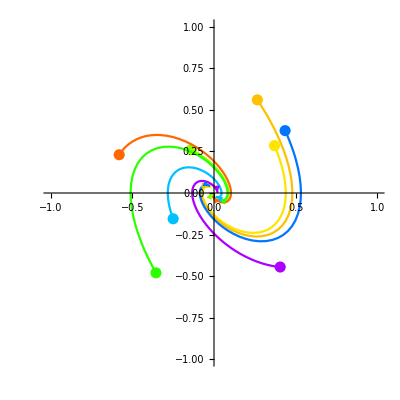
{EquationTrekkerState["tut0.16.","{}",TrekData["0.1u'", <>]
TrekData["0.1u'", <>]
TrekData["0.1u'", <>]
TrekData["0.1u'", <>]
TrekData["0.1u'", <>]
TrekData["0.1u'", <>]
TrekData["0.1u'", <>]
TrekData["0.1u'", <>], <>],-Graphics-}

```mathematica
EquationTrekker[u''[t]-(a+d)*u'[t]+(d*a-b*c)*u[t]==0,u,{t,0.1,6.0}]
```

#### Nodal Sink

```mathematica
FindInstance[(a+d)^2 - 4(a*d-b*c)>0 && ((a +d)/2 + Sqrt[(a+d)^2 - 4(a*d-b*c)]/2) * ((a +d)/2 - Sqrt[(a+d)^2 - 4(a*d-b*c)]/2) > 0 && ((a +d)/2 + Sqrt[(a+d)^2 - 4(a*d-b*c)]/2) + ((a +d)/2 - Sqrt[(a+d)^2 - 4(a*d-b*c)]/2) < 0,{a,b,c,d}]
```

{{a→-1,b→1/8,c→-1,d→0}}

```mathematica
a = -1;b = 1/8;c =-1;d = 0;
```

PropertyValue::pvobj: canvas is not an object with properties.

PropertyValue::pvobj: trekPane is not an object with properties.

PropertyValue::poi: -- Message text not found -- (PropertyValue[{canvas,canvasPane,All},Name→trekPane]) (1)

PropertyValue::poi: -- Message text not found -- (PropertyValue[{trekPane,trekController,All},Name→trekController]) (1)

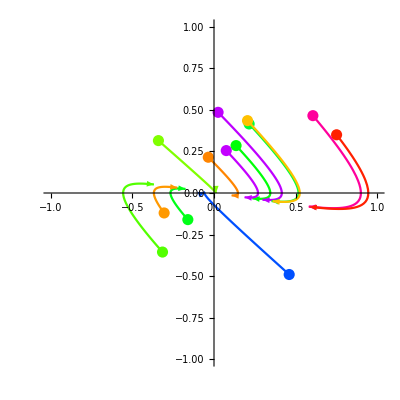
{EquationTrekkerState["u[t]/8ut0.16.","{}",TrekData["0.1u'", <>]
TrekData["0.1u'", <>]
TrekData["0.1u'", <>]
TrekData["0.1u'", <>]
TrekData["0.1u'", <>]
TrekData["0.1u'", <>]
TrekData["0.1u'", <>]
TrekData["0.1u'", <>]
TrekData["0.1u'", <>]
TrekData["0.1u'", <>]
TrekData["0.1u'", <>]
TrekData["0.1u'", <>]
TrekData["0.1u'", <>], <>],-Graphics-}

```mathematica
EquationTrekker[u''[t]-(a+d)*u'[t]+(d*a-b*c)*u[t]==0,u,{t,0.1,6.0}]
```

### Spiral Source

```mathematica
FindInstance[(a+d)^2 - 4(a*d-b*c)<0 &&  (a+ d) > 0,{a,b,c,d}]
```

{{a→1,b→1,c→-1,d→0}}

```mathematica
a = 1;b = 1;c =-1;d = 0;
```

PropertyValue::pvobj: canvas is not an object with properties.

PropertyValue::pvobj: trekPane is not an object with properties.

PropertyValue::poi: -- Message text not found -- (PropertyValue[{canvas,canvasPane,All},Name→trekPane]) (1)

PropertyValue::poi: -- Message text not found -- (PropertyValue[{trekPane,trekController,All},Name→trekController]) (1)

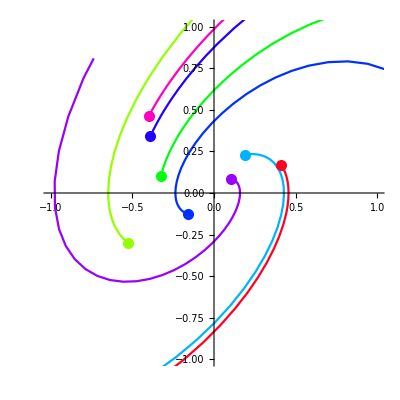
{EquationTrekkerState["tut0.16.","{}",TrekData["0.1u'", <>]
TrekData["0.1u'", <>]
TrekData["0.1u'", <>]
TrekData["0.1u'", <>]
TrekData["0.1u'", <>]
TrekData["0.1u'", <>]
TrekData["0.1u'", <>]
TrekData["0.1u'", <>], <>],-Graphics-}

```mathematica
EquationTrekker[u''[t]-(a+d)*u'[t]+(d*a-b*c)*u[t]==0,u,{t,0.1,6.0}]
```

#### Nodal Source:

```mathematica
FindInstance[(a+d)^2 - 4(a*d-b*c)>0 && ((a +d)/2 + Sqrt[(a+d)^2 - 4(a*d-b*c)]/2) * ((a +d)/2 - Sqrt[(a+d)^2 - 4(a*d-b*c)]/2) > 0 && ((a +d)/2 + Sqrt[(a+d)^2 - 4(a*d-b*c)]/2) + ((a +d)/2 - Sqrt[(a+d)^2 - 4(a*d-b*c)]/2) > 0,{a,b,c,d}]
```

{{a→1,b→1/8,c→-1,d→0}}

```mathematica
a = 1;b = 1/8;c =-1;d = 0;
```

PropertyValue::pvobj: canvas is not an object with properties.

PropertyValue::pvobj: trekPane is not an object with properties.

PropertyValue::poi: -- Message text not found -- (PropertyValue[{canvas,canvasPane,All},Name→trekPane]) (1)

PropertyValue::poi: -- Message text not found -- (PropertyValue[{trekPane,trekController,All},Name→trekController]) (1)

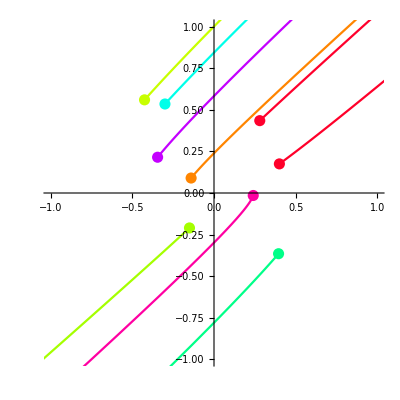
{EquationTrekkerState["u[t]/8ut0.16.","{}",TrekData["0.1u'", <>]
TrekData["0.1u'", <>]
TrekData["0.1u'", <>]
TrekData["0.1u'", <>]
TrekData["0.1u'", <>]
TrekData["0.1u'", <>]
TrekData["0.1u'", <>]
TrekData["0.1u'", <>]
TrekData["0.1u'", <>], <>],-Graphics-}

```mathematica
EquationTrekker[u''[t]-(a+d)*u'[t]+(d*a-b*c)*u[t]==0,u,{t,0.1,6.0}]
```

### Saddle

```mathematica
FindInstance[(a+d)^2 - 4(a*d-b*c)>0 && ((a +d)/2 + Sqrt[(a+d)^2 - 4(a*d-b*c)]/2) * ((a +d)/2 - Sqrt[(a+d)^2 - 4(a*d-b*c)]/2) < 0 ,{a,b,c,d}]
```

{{a→-1,b→-1,c→-1,d→0}}

```mathematica
a = -1;b = -1;c =-1;d = 0;
```

PropertyValue::pvobj: canvas is not an object with properties.

PropertyValue::pvobj: trekPane is not an object with properties.

PropertyValue::poi: -- Message text not found -- (PropertyValue[{canvas,canvasPane,All},Name→trekPane]) (1)

PropertyValue::poi: -- Message text not found -- (PropertyValue[{trekPane,trekController,All},Name→trekController]) (1)

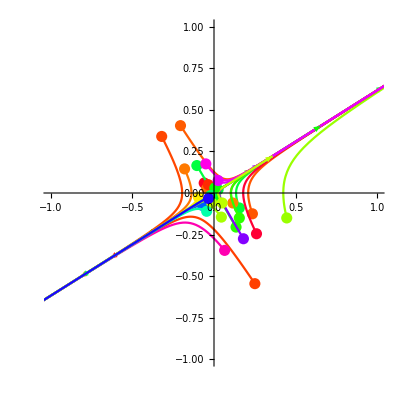
{EquationTrekkerState["-u[t]ut0.16.","{}",TrekData["0.1u'", <>]
TrekData["0.1u'", <>]
TrekData["0.1u'", <>]
TrekData["0.1u'", <>]
TrekData["0.1u'", <>]
TrekData["0.1u'", <>]
TrekData["0.1u'", <>]
TrekData["0.1u'", <>]
TrekData["0.1u'", <>]
TrekData["0.1u'", <>]
TrekData["0.1u'", <>]
TrekData["0.1u'", <>]
TrekData["0.1u'", <>]
TrekData["0.1u'", <>]
TrekData["0.1u'", <>]
TrekData["0.1u'", <>]
TrekData["0.1u'", <>]
TrekData["0.1u'", <>]
TrekData["0.1u'", <>]
TrekData["0.1u'", <>]
TrekData["0.1u'", <>]
TrekData["0.1u'", <>]
TrekData["0.1u'", <>]
TrekData["0.1u'", <>]
TrekData["0.1u'", <>]
TrekData["0.1u'", <>]
TrekData["0.1u'", <>]
TrekData["0.1u'", <>]
TrekData["0.1u'", <>]
TrekData["0.1u'", <>]
TrekData["0.1u'", <>], <>],-Graphics-}

```mathematica
EquationTrekker[u''[t]-(a+d)*u'[t]+(d*a-b*c)*u[t]==0,u,{t,0.1,6.0}]
```

### Center

```mathematica
FindInstance[(a+d)^2 - 4(a*d-b*c)<0 && (a + d) == 0,{a,b,c,d}]
```

{{a→0,b→1,c→-1,d→0}}

```mathematica
a = 0;b = 1;c =-1;d = 0;
```

PropertyValue::pvobj: canvas is not an object with properties.

PropertyValue::pvobj: trekPane is not an object with properties.

PropertyValue::poi: -- Message text not found -- (PropertyValue[{canvas,canvasPane,All},Name→trekPane]) (1)

PropertyValue::poi: -- Message text not found -- (PropertyValue[{trekPane,trekController,All},Name→trekController]) (1)

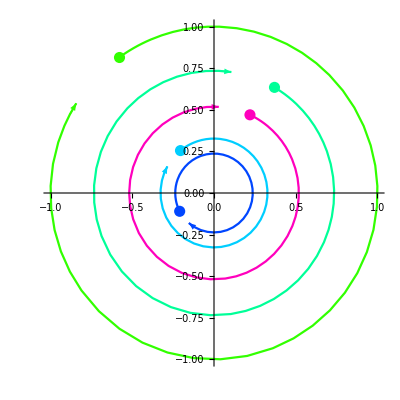
{EquationTrekkerState["tut0.16.","{}",TrekData["0.1u'", <>]
TrekData["0.1u'", <>]
TrekData["0.1u'", <>]
TrekData["0.1u'", <>]
TrekData["0.1u'", <>], <>],-Graphics-}

```mathematica
EquationTrekker[u''[t]-(a+d)*u'[t]+(d*a-b*c)*u[t]==0,u,{t,0.1,6.0}]
```

### Degenerate Nodal Source

```mathematica
FindInstance[(a+d)^2 - 4(a*d-b*c)==0 && (a + d) > 0,{a,b,c,d}]
```

{{a→7/8,b→0,c→0,d→7/8}}

```mathematica
a = 7/8;b = 0;c =0;d = 7/8;
```

PropertyValue::pvobj: canvas is not an object with properties.

PropertyValue::pvobj: trekPane is not an object with properties.

PropertyValue::poi: -- Message text not found -- (PropertyValue[{canvas,canvasPane,All},Name→trekPane]) (1)

PropertyValue::poi: -- Message text not found -- (PropertyValue[{trekPane,trekController,All},Name→trekController]) (1)

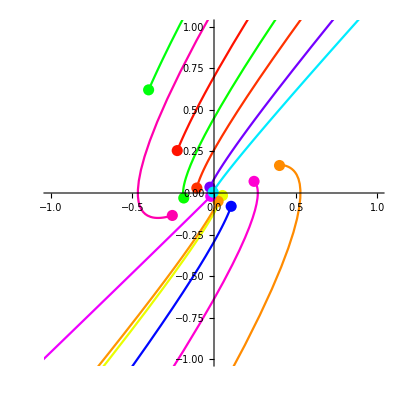
{EquationTrekkerState["(49 u[t])/64ut0.16.","{}",TrekData["0.1u'", <>]
TrekData["0.1u'", <>]
TrekData["0.1u'", <>]
TrekData["0.1u'", <>]
TrekData["0.1u'", <>]
TrekData["0.1u'", <>]
TrekData["0.1u'", <>]
TrekData["0.1u'", <>]
TrekData["0.1u'", <>]
TrekData["0.1u'", <>]
TrekData["0.1u'", <>]
TrekData["0.1u'", <>]
TrekData["0.1u'", <>], <>],-Graphics-}

```mathematica
EquationTrekker[u''[t]-(a+d)*u'[t]+(d*a-b*c)*u[t]==0,u,{t,0.1,6.0}]
```

### Degenerate Nodal Sink

```mathematica
FindInstance[(a+d)^2 - 4(a*d-b*c)==0 && (a + d) < 0,{a,b,c,d}]
```

{{a→-1,b→0,c→0,d→-1}}

```mathematica
a = -1;b = 0;c =0;d = -1;
```

PropertyValue::pvobj: canvas is not an object with properties.

PropertyValue::pvobj: trekPane is not an object with properties.

PropertyValue::poi: -- Message text not found -- (PropertyValue[{canvas,canvasPane,All},Name→trekPane]) (1)

PropertyValue::poi: -- Message text not found -- (PropertyValue[{trekPane,trekController,All},Name→trekController]) (1)

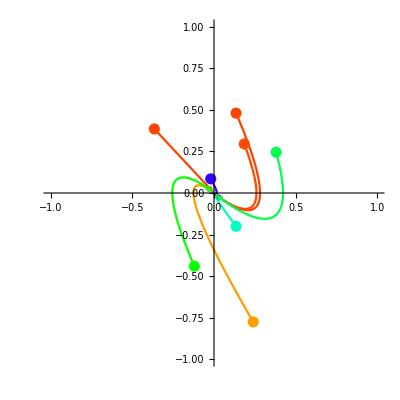
{EquationTrekkerState["tut0.16.","{}",TrekData["0.1u'", <>]
TrekData["0.1u'", <>]
TrekData["0.1u'", <>]
TrekData["0.1u'", <>]
TrekData["0.1u'", <>]
TrekData["0.1u'", <>]
TrekData["0.1u'", <>]
TrekData["0.1u'", <>], <>],-Graphics-}

```mathematica
EquationTrekker[u''[t]-(a+d)*u'[t]+(d*a-b*c)*u[t]==0,u,{t,0.1,6.0}]
```

### Unstable Saddle–Node

```mathematica
FindInstance[(a*d-b*c)==0 && (a + d) > 0,{a,b,c,d}]
```

```mathematica
{{a->0,b->0,c->0,d->1}}
```

```mathematica
{{a->0,b->0,c->0,d->1}}
```

```mathematica
a = 0;b = 0;c =0;d = 1;
```

PropertyValue::pvobj: canvas is not an object with properties.

PropertyValue::pvobj: trekPane is not an object with properties.

PropertyValue::poi: -- Message text not found -- (PropertyValue[{canvas,canvasPane,All},Name→trekPane]) (1)

PropertyValue::poi: -- Message text not found -- (PropertyValue[{trekPane,trekController,All},Name→trekController]) (1)

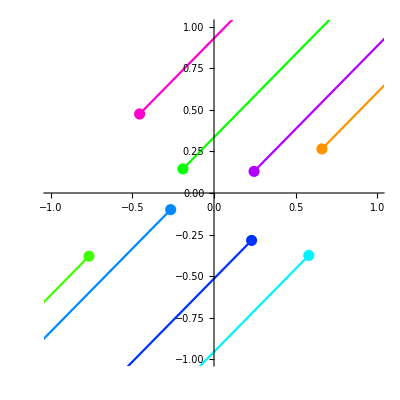
{EquationTrekkerState["u'ut0.16.","{}",TrekData["0.1u'", <>]
TrekData["0.1u'", <>]
TrekData["0.1u'", <>]
TrekData["0.1u'", <>]
TrekData["0.1u'", <>]
TrekData["0.1u'", <>]
TrekData["0.1u'", <>]
TrekData["0.1u'", <>], <>],-Graphics-}

```mathematica
EquationTrekker[u''[t]-(a+d)*u'[t]+(d*a-b*c)*u[t]==0,u,{t,0.1,6.0}]
```

### Stable Saddle–Node

```mathematica
FindInstance[(a*d-b*c)==0 && (a + d) < 0,{a,b,c,d}]
```

```mathematica
{{a->0,b->0,c->0,d->-1}}
```

```mathematica
a =  0;b = 0;c =0;d = -1;
```

PropertyValue::pvobj: canvas is not an object with properties.

PropertyValue::pvobj: trekPane is not an object with properties.

PropertyValue::poi: -- Message text not found -- (PropertyValue[{canvas,canvasPane,All},Name→trekPane]) (1)

PropertyValue::poi: -- Message text not found -- (PropertyValue[{trekPane,trekController,All},Name→trekController]) (1)

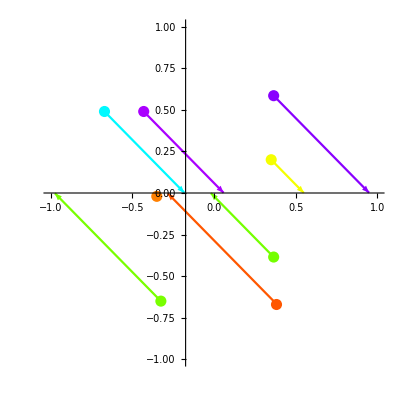
{EquationTrekkerState["u'ut0.16.","{}",TrekData["0.1u'", <>]
TrekData["0.1u'", <>]
TrekData["0.1u'", <>]
TrekData["0.1u'", <>]
TrekData["0.1u'", <>]
TrekData["0.1u'", <>]
TrekData["0.1u'", <>]
TrekData["0.1u'", <>], <>],-Graphics-}

```mathematica
EquationTrekker[u''[t]-(a+d)*u'[t]+(d*a-b*c)*u[t]==0,u,{t,0.1,6.0}]
```